```mathematica
(*Import packages*)
(*<< PVReduce`*)
(*Remove[PVReduce`Dot];*)
$LoadAddOns={"FeynArts"};
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

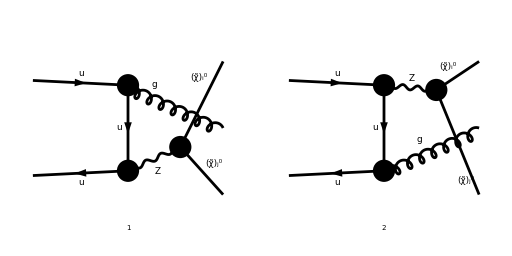

```mathematica
EmissionDiagrams = InsertFields[CreateTopologies[0, 2->3], {F[3, {1,α}], -F[3, {1,β}]} -> {F[11, {i}],V[5,{a}], F[11, {j}]}, InsertionLevel -> {Classes}, Model -> MSSMQCD,Restrictions->{NoLightFHCoupling,NoElectronHCoupling,NoSUSYParticles}];
Paint[EmissionDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

```mathematica
Subscript[M, gluon][0]=FCFAConvert[CreateFeynAmp[EmissionDiagrams], IncomingMomenta->{ki,kj}, OutgoingMomenta->{pi,k,pj},ChangeDimension->D,UndoChiralSplittings->True,List->True,SMP->True,DropSumOver->True,LorentzIndexNames->{μ,ν}]//.AmpSimplifyRules;
```

```mathematica
Subscript[M, gluon][1]=Simplify/@(Subscript[M, gluon][0]/.ZSimplifyRules/.QSimplifyRules/.SuperChargeRules);
```

```mathematica
Subscript[M̄, gluon][1]=ConjugateAmplitude[Subscript[M, gluon][1]];
```

```mathematica
FCClearScalarProducts[];
ScalarProduct[k,k]=0;
SetMandelstam[m2,{ki,kj,-pi,-pj,-k},{0,0,MNeu[i],MNeu[j],0}];
SetMandelstamParameters[s,t,u,MNeu[i]^2+MNeu[j]^2-(1-z)s];
```

```mathematica
$Assumptions={ z>0,z<1,y>0,y<1};
```

```mathematica
FreeProducts={
m2[1,2]->s,
m2[1,3]->t1,
m2[3,4]->s z,
m2[3,5]->mi5,
m2[1,5]->-s(1-z)(1-y),
m2[2,5]->-s(1-z)y
(*m2[1,2]->s,
m2[1,3]->t1,
m2[1,4]->u1,
m2[2,3]->u2,
m2[2,4]->t2*)
};
ConstrainedProducts={
m2[2,3]->2 MNeu[i]^2+MNeu[j]^2-mi5-s z-t1,
m2[1,4]->MNeu[i]^2+MNeu[j]^2-s(1-y)z-s y-t1,
m2[2,4]->-MNeu[i]^2+mi5-s(1-y)(1-z)+t1,
m2[4,5]->MNeu[i]^2+MNeu[j]^2-mi5+(1-z)s
(*m2[1,5]->MNeu[i]^2+MNeu[j]^2-s-t1-u1,
m2[2,5]->MNeu[i]^2+MNeu[j]^2-s-t2-u2,
m2[3,4]->2 MNeu[i]^2+2 MNeu[j]^2-s-t1-t2-u1-u2,
m2[3,5]->-MNeu[j]^2+s+t2+u1,
m2[4,5]->-MNeu[i]^2+s+t1+u2*)
};
ProductRelations={
m2[1,2]->m2[3,4]+m2[3,5]+m2[4,5]-MNeu[i]^2-MNeu[j]^2,
m2[1,3]->m2[2,4]+m2[2,5]+m2[4,5]-MNeu[j]^2,
m2[1,4]->m2[2,3]+m2[2,5]+m2[3,5]-MNeu[i]^2,
m2[1,5]->m2[2,3]+m2[2,4]+m2[3,4]-MNeu[i]^2-MNeu[j]^2,
m2[2,3]->m2[1,4]+m2[1,5]+m2[4,5]-MNeu[j]^2,
m2[2,4]->m2[1,3]+m2[1,5]+m2[3,5]-MNeu[i]^2,
m2[2,5]->m2[1,3]+m2[1,4]+m2[3,4]-MNeu[i]^2-MNeu[j]^2,
m2[3,4]->m2[1,2]+m2[1,5]+m2[2,5],
m2[3,5]->m2[1,2]+m2[1,4]+m2[2,4]-MNeu[j]^2,
m2[4,5]->m2[1,2]+m2[1,3]+m2[2,3]-MNeu[i]^2
};
AngularSubs={
mi5->1/(2z)((MNeu[i]^2-MNeu[j]^2)+(MNeu[i]^2+MNeu[j]^2)z+s z(1-z)+Sqrt[s^2 z^2+MNeu[i]^4+MNeu[j]^4-2(s z MNeu[i]^2+s z MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)]cTheta)
};
```

```mathematica
MakeBoxes[m2,TraditionalForm]=SuperscriptBox["m",2];
MakeBoxes[t1,TraditionalForm]=SubscriptBox["t",1];
MakeBoxes[t2,TraditionalForm]=SubscriptBox["t",2];
MakeBoxes[u1,TraditionalForm]=SubscriptBox["u",1];
MakeBoxes[u2,TraditionalForm]=SubscriptBox["u",2];
MakeBoxes[cTheta, TraditionalForm]=RowBox[{"cos","(","θ",")"}];
MakeBoxes[sTheta, TraditionalForm]=RowBox[{"sin","(","θ",")"}];
MakeBoxes[cPhi, TraditionalForm]=RowBox[{"cos","(","ϕ",")"}];
```

```mathematica
ReduceScalars[expr_]:=expr/.FreeProducts/.ConstrainedProducts
RewriteScalars[expr_]:=expr/.ProductRelations
RewriteAndReduceScalars[expr_]:=expr/.ProductRelations//ReduceScalars
```

```mathematica
(*Igluon[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],2]/.{Index[Sfermion,6]->A} ,
Part[Subscript[M̄, gluon][1],2]/.{Index[Sfermion,6]->B}
]/.SuperChargeRules,k,0];*)
```

```mathematica
(*Igluon[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Igluon[0]]]//ReduceScalars];*)
```

```mathematica
(*Igluon[2]=Simplify[Collect2[Expand[Igluon[1]//ReduceScalars]/.SuperChargeRules,{Qtu,QtuC,Cq Opp}]/.SuperChargeRules];*)
```

```mathematica
(*Igluon[3]=Simplify[Collect2[Expand[Igluon[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq,Opp}]/.SuperChargeRules]*)
```

```mathematica
FRH[DiracSimplify[(FermionSpinSum[#1]&)[Part[Subscript[M, gluon][1],1]Part[Subscript[M̄, gluon][1],1]]]]
```

```mathematica
CalcColorFactor[SelectFree2[%/.SuperChargeRules,DiracTrace]//DoPolarizationSums[#,k,0]&]//Simplify
```

(D-2) m^2(1,5) (-C_A) C_F g_s^2 g_W^4 (C_L^2+C_R^2) (1/(k_j-p_i-p_j)^2)^2 (1/((p_i+p_j)^2-m_Z^2))^2 (Conjugate[(O_ij^L)] ((m_i^2 ((D-2) m^2(1,2)+D m^2(1,5)-D m^2(3,4)-4 m^2(1,5)+2 m^2(3,4)-4 m^2(4,5)+4 m_j^2)+m_j^2 ((D-4) m^2(1,2)+(D-2) m^2(1,5)-D m^2(3,4)-4 m^2(2,3)+2 m^2(3,4))+D (m^2(3,4))^2-D m^2(1,2) m^2(3,4)-D m^2(1,5) m^2(3,4)-2 (m^2(3,4))^2+2 m^2(1,2) m^2(3,4)+2 m^2(1,5) m^2(3,4)+2 m^2(2,3) m^2(3,4)+2 m^2(4,5) m^2(3,4)+2 m^2(1,2) m^2(1,5)-2 m^2(1,2) m^2(2,3)-2 m^2(1,5) m^2(4,5)+4 m^2(2,3) m^2(4,5)) Conjugate[(O_ij^R)]+2 (D-2) (m^2(1,2)+m^2(1,5)-m^2(3,4)) m_i m_j O_ij^R)+O_ij^L (2 (D-2) (m^2(1,2)+m^2(1,5)-m^2(3,4)) m_i m_j Conjugate[(O_ij^R)]+O_ij^R (m_i^2 ((D-2) m^2(1,2)+D m^2(1,5)-D m^2(3,4)-4 m^2(1,5)+2 m^2(3,4)-4 m^2(4,5)+4 m_j^2)+m_j^2 ((D-4) m^2(1,2)+(D-2) m^2(1,5)-D m^2(3,4)-4 m^2(2,3)+2 m^2(3,4))+D (m^2(3,4))^2-D m^2(1,2) m^2(3,4)-D m^2(1,5) m^2(3,4)-2 (m^2(3,4))^2+2 m^2(1,2) m^2(3,4)+2 m^2(1,5) m^2(3,4)+2 m^2(2,3) m^2(3,4)+2 m^2(4,5) m^2(3,4)+2 m^2(1,2) m^2(1,5)-2 m^2(1,2) m^2(2,3)-2 m^2(1,5) m^2(4,5)+4 m^2(2,3) m^2(4,5))))

```mathematica
Itt[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],1],
Part[Subscript[M̄, gluon][1],1]
]/.SuperChargeRules,k,0];
Iuu[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],2],
Part[Subscript[M̄, gluon][1],2]
]/.SuperChargeRules,k,0];
Itu[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],1],
Part[Subscript[M̄, gluon][1],2]
]/.SuperChargeRules,k,0];
Iut[0]=DoPolarizationSums[SquareAmplitudes[
Part[Subscript[M, gluon][1],2] ,
Part[Subscript[M̄, gluon][1],1]
]/.SuperChargeRules,k,0];
```

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

```mathematica
Itt[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Itt[0]]]//ReduceScalars];
Iuu[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Iuu[0]]]//ReduceScalars];
Itu[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Itu[0]]]//ReduceScalars];
Iut[1]=Simplify[(SelectFree2[CalcColorFactor[#1],DiracTrace]&)[FeynAmpDenominatorExplicit[Iut[0]]]//ReduceScalars];
```

```mathematica
Itt[2]=Simplify[Collect[Expand[Itt[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq[args__],Opp[args__]}]/.SuperChargeRules];
Iuu[2]=Simplify[Collect[Expand[Iuu[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq[args__],Opp[args__]}]/.SuperChargeRules];
Itu[2]=Simplify[Collect[Expand[Itu[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq[args__],Opp[args__]}]/.SuperChargeRules];
Iut[2]=Simplify[Collect[Expand[Iut[1]/.{Conjugate[Opp[args__,L]]->-Opp[args,R],Conjugate[Opp[args__,R]]->-Opp[args,L]}]/.SuperChargeRules,{Cq[args__],Opp[args__]}]/.SuperChargeRules];
```

```mathematica
Prefac=2 CA CF SMP["g_s"]^2 SMP["g_W"]^4;
```

```mathematica
Itt[3]=Itt[2]/Prefac;
Iuu[3]=Iuu[2]/Prefac;
Itu[3]=Itu[2]/Prefac;
Iut[3]=Iut[2]/Prefac;
```

```mathematica
Itot =Simplify[Itt[3]+Iuu[3]+Itu[3]+Iut[3]]
```

1/(s (z-1)^2)2 (-((2 s z (Conjugate[(C_jSfe6^L)])^2 m_i m_j (C_iSfe6^L)^2+2 s z (Conjugate[(C_iSfe6^R)])^2 (C_jSfe6^R)^2 m_i m_j+Conjugate[(Q_Sfe6^RL)] ((2 (D-2) y (z-1)-(D-6) z) m_i^4+(2 D s z^2-10 s z^2-3 D s y z^2+10 s y z^2+2 D mi5 z-10 mi5 z-2 D s z+10 s z-3 D mi5 y z+10 mi5 y z+5 D s y z-18 s y z+(D (y-1) (z-1)-6 y (z-1)+8 z-2) m_j^2+3 D mi5 y-10 mi5 y-2 D s y+8 s y+t_1 (4 y (z-1)-10 z+D (-2 y (z-1)+z-1)+2)) m_i^2+2 (-z y+y+z-1) m_j^4-D s^2 z^3+4 s^2 z^3+D s^2 y z^3-4 s^2 y z^3+2 D s^2 z^2-8 s^2 z^2-2 D mi5 s z^2+8 mi5 s z^2-D s t_1 z^2+8 s t_1 z^2-2 D s^2 y z^2+8 s^2 y z^2+2 D mi5 s y z^2-8 mi5 s y z^2+2 D s t_1 y z^2-8 s t_1 y z^2+(2 t_1 (2 y (z-1)-3 z+1)-s (y-1) (D (z-1)-6 z+4) (z-1)+mi5 (6 y (z-1)-6 z+D (-z y+y+z-1)+4)) m_j^2+D mi5 t_1-4 mi5 t_1-D s t_1+4 s t_1-D mi5^2 y+4 mi5^2 y+D mi5 s y-4 mi5 s y-2 D mi5 t_1 y+8 mi5 t_1 y+2 D s t_1 y-8 s t_1 y-D mi5^2 z+4 mi5^2 z-D s^2 z+4 s^2 z+4 t_1^2 z+2 D mi5 s z-8 mi5 s z-D mi5 t_1 z+8 mi5 t_1 z+2 D s t_1 z-8 s t_1 z+D mi5^2 y z-4 mi5^2 y z+D s^2 y z-4 s^2 y z-3 D mi5 s y z+12 mi5 s y z+2 D mi5 t_1 y z-8 mi5 t_1 y z-4 D s t_1 y z+16 s t_1 y z) Q_Sfe6^LR)/((y-1) y (t_1-m_((q̃)_Sfe6)^2) (-2 m_i^2-m_j^2+m_((q̃)_Sfe6)^2+mi5+t_1+s z)))-(2 s z (Conjugate[(C_jSfe6^R)])^2 m_i m_j (C_iSfe6^R)^2+2 s z (Conjugate[(C_iSfe6^L)])^2 (C_jSfe6^L)^2 m_i m_j+Conjugate[(Q_Sfe6^LR)] ((2 (D-2) y (z-1)-(D-6) z) m_i^4+(2 D s z^2-10 s z^2-3 D s y z^2+10 s y z^2+2 D mi5 z-10 mi5 z-2 D s z+10 s z-3 D mi5 y z+10 mi5 y z+5 D s y z-18 s y z+(D (y-1) (z-1)-6 y (z-1)+8 z-2) m_j^2+3 D mi5 y-10 mi5 y-2 D s y+8 s y+t_1 (4 y (z-1)-10 z+D (-2 y (z-1)+z-1)+2)) m_i^2+2 (-z y+y+z-1) m_j^4-D s^2 z^3+4 s^2 z^3+D s^2 y z^3-4 s^2 y z^3+2 D s^2 z^2-8 s^2 z^2-2 D mi5 s z^2+8 mi5 s z^2-D s t_1 z^2+8 s t_1 z^2-2 D s^2 y z^2+8 s^2 y z^2+2 D mi5 s y z^2-8 mi5 s y z^2+2 D s t_1 y z^2-8 s t_1 y z^2+(2 t_1 (2 y (z-1)-3 z+1)-s (y-1) (D (z-1)-6 z+4) (z-1)+mi5 (6 y (z-1)-6 z+D (-z y+y+z-1)+4)) m_j^2+D mi5 t_1-4 mi5 t_1-D s t_1+4 s t_1-D mi5^2 y+4 mi5^2 y+D mi5 s y-4 mi5 s y-2 D mi5 t_1 y+8 mi5 t_1 y+2 D s t_1 y-8 s t_1 y-D mi5^2 z+4 mi5^2 z-D s^2 z+4 s^2 z+4 t_1^2 z+2 D mi5 s z-8 mi5 s z-D mi5 t_1 z+8 mi5 t_1 z+2 D s t_1 z-8 s t_1 z+D mi5^2 y z-4 mi5^2 y z+D s^2 y z-4 s^2 y z-3 D mi5 s y z+12 mi5 s y z+2 D mi5 t_1 y z-8 mi5 t_1 y z-4 D s t_1 y z+16 s t_1 y z) Q_Sfe6^RL)/((y-1) y (t_1-m_((q̃)_Sfe6)^2) (-2 m_i^2-m_j^2+m_((q̃)_Sfe6)^2+mi5+t_1+s z))+((D-2) (z-1) (t_1-m_i^2) (m_i^2-mi5+s-s z) (Conjugate[(Q_Sfe6^LL)] Q_Sfe6^LL+Conjugate[(Q_Sfe6^LR)] Q_Sfe6^LR+Conjugate[(Q_Sfe6^RL)] Q_Sfe6^RL+Conjugate[(Q_Sfe6^RR)] Q_Sfe6^RR))/(y (t_1-m_((q̃)_Sfe6)^2)^2)-((D-2) (z-1) (-m_i^2+mi5+s (z-1)) (-m_i^2-m_j^2+mi5+t_1+s z) (Conjugate[(Q_Sfe6^LL)] Q_Sfe6^LL+Conjugate[(Q_Sfe6^LR)] Q_Sfe6^LR+Conjugate[(Q_Sfe6^RL)] Q_Sfe6^RL+Conjugate[(Q_Sfe6^RR)] Q_Sfe6^RR))/((y-1) (-2 m_i^2-m_j^2+m_((q̃)_Sfe6)^2+mi5+t_1+s z)^2))

```mathematica
SoftLimit[expr_]:=ReplaceAll[TrickMandelstam[ReplaceAll[expr,{t1->t+Sqrt[s^2+MNeu[i]^4+MNeu[j]^4-2(s MNeu[i]^2+s MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)](Sqrt[y(1-y)]sTheta cPhi - y cTheta),mi5->MNeu[i]^2}],{s,t,u,MNeu[i]^2+MNeu[j]^2}]//Simplify,{z->1}];
CollinearLimit1[expr_]:=ReplaceAll[ReplaceAll[expr,{t1->(MNeu[i]^2+MNeu[j]^2-s z+Sqrt[s^2 z^2+MNeu[i]^4+MNeu[j]^4-2(s z MNeu[i]^2+s z MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)]cTheta)/2}]//Simplify,{y->0}];
CollinearLimit2[expr_]:=ReplaceAll[ReplaceAll[expr,{t1->(2 MNeu[j]^2+MNeu[i]^2 z-s z-Sqrt[s^2 z^2+MNeu[i]^4+MNeu[j]^4-2(s z MNeu[i]^2+s z MNeu[j]^2+MNeu[i]^2 MNeu[j]^2)]cTheta)/(2z)}]//Simplify,{y->1}];
SoftCollinearLimit={y->0,z->1};
```

```mathematica
Iuu[3]//SoftLimit
Iuu[3]//CollinearLimit1//Simplify
Iuu[3]//CollinearLimit2//Simplify
Iuu[3]//CollinearLimit1//SoftLimit//Simplify
Iuu[3]//CollinearLimit2//SoftLimit//Simplify
(SoftLimit[#1]//CollinearLimit1&)[Iuu[3]]
(SoftLimit[#1]//CollinearLimit2&)[Iuu[3]]
```

-(2 (D-2) (Q_Sfe6^LR Conjugate[(Q_Sfe6^LR)]+Q_Sfe6^RL Conjugate[(Q_Sfe6^RL)]+Q_Sfe6^LL Conjugate[(Q_Sfe6^LL)]+Q_Sfe6^RR Conjugate[(Q_Sfe6^RR)]) (sin(θ) cos(ϕ) √(-((y-1) y ((t+u)^2-4 m_i^2 m_j^2)))-y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)-m_j^2+s+t))/((y-1) (-m_((q̃)_Sfe6)^2-sin(θ) cos(ϕ) √(-((y-1) y ((t+u)^2-4 m_i^2 m_j^2)))+y cos(θ) √((t+u)^2-4 m_i^2 m_j^2)+u)^2)

(4 (D-2) (Q_Sfe6^LR Conjugate[(Q_Sfe6^LR)]+Q_Sfe6^RL Conjugate[(Q_Sfe6^RL)]+Q_Sfe6^LL Conjugate[(Q_Sfe6^LL)]+Q_Sfe6^RR Conjugate[(Q_Sfe6^RR)]) (-m_i^2+mi5+s (z-1)) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2-m_j^2+2 mi5+s z))/(s (z-1) (2 m_((q̃)_Sfe6)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 m_i^2-m_j^2+2 mi5+s z)^2)

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

(4 (D-2) (Q_Sfe6^LR Conjugate[(Q_Sfe6^LR)]+Q_Sfe6^RL Conjugate[(Q_Sfe6^RL)]+Q_Sfe6^LL Conjugate[(Q_Sfe6^LL)]+Q_Sfe6^RR Conjugate[(Q_Sfe6^RR)]) (cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)+m_i^2-m_j^2+s))/((2 m_((q̃)_Sfe6)^2+cos(θ) √(-2 m_i^2 (m_j^2+s)+m_i^4+(s-m_j^2)^2)-m_i^2-m_j^2+s)^2)

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

(4 (D-2) (Q_Sfe6^LR Conjugate[(Q_Sfe6^LR)]+Q_Sfe6^RL Conjugate[(Q_Sfe6^RL)]+Q_Sfe6^LL Conjugate[(Q_Sfe6^LL)]+Q_Sfe6^RR Conjugate[(Q_Sfe6^RR)]) (-m_i^2+mi5+s (z-1)) (cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-m_i^2-m_j^2+2 mi5+s z))/(s (z-1) (2 m_((q̃)_Sfe6)^2+cos(θ) √(-2 m_i^2 (m_j^2+s z)+m_i^4+(m_j^2-s z)^2)-3 m_i^2-m_j^2+2 mi5+s z)^2)

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
%//.{z->1}//FullSimplify
```

ComplexInfinity